## Load package

```mathematica
(* run once to install EcoEvo package v1.7.2 *)
PacletInstall["https://github.com/cklausme/EcoEvo/releases/download/1.7.2/EcoEvo-1.7.2.paclet"]
```

PacletInstall::samevers: A paclet named EcoEvo with the same version number (1.7.2) is already installed. Use PacletUninstall to remove the existing version first, or call PacletInstall with ForceVersionInstall -> True.

```mathematica
<<EcoEvo`
```

EcoEvo Package Version 1.7.2 (September 1, 2023)
Christopher A. Klausmeier <christopher.klausmeier@gmail.com>

```mathematica
Charting`$InteractiveHighlighting=False;
```

## Various functions

```mathematica
(* find equilibrium TAD *)
Clear[FindTAD];
FindTAD:=Chop[FinalSlice[EcoSim[traits,ics,10^10]]];
```

```mathematica
(* plot a TAD *)
Clear[PlotTAD];
PlotTAD[traits_,sol_,opts___?OptionQ]:=
PlotGuild[traits,sol,opts,Logged->True,PlotRange->All,Filling->None,Joined->True,PlotMarkers->None]
```

```mathematica
(* split a TAD into peaks *)
Clear[SplitPeaks];
SplitPeaks[dist_List]:=Module[{mins,maxs},
maxs=FindPeaks[dist][[All,1]];
mins=Union[Join[{1},FindPeaks[-dist][[All,1]],{Length[dist]}]];
(*Print["mins: ",mins," maxs:",maxs];*)
Table[
(*Print[dist[[Ceiling[mins[[i]]];;Floor[mins[[i+1]]]]]];*)
{maxs[[i]],Total[dist[[Ceiling[mins[[i]]];;Floor[mins[[i+1]]]]]]
-If[mins[[i]]!=1&&IntegerQ[mins[[i]]],(*Print["* ",-dist[[mins[[i]]]]/2];*)dist[[mins[[i]]]]/2,0]
-If[mins[[i+1]]!=Length[dist]&&IntegerQ[mins[[i+1]]],(*Print["** ",-dist[[mins[[i+1]]]]/2];*)dist[[mins[[i+1]]]]/2,0]}
,{i,Length[mins]-1}]
]
```

## Model definition

Note: we use capital Greek symbols Ν (typed Esc-N-Esc) as N, Ε (typed Esc-E-Esc) as E, ΕR (typed Esc-E-EscR) as ER, to avoid Mathematica’s built-in symbols N and E.

```mathematica
(* eqns. 1 *)
SetModel[{
Guild[Ν]->{Equation:>Subscript[Ν, i](μ[Subscript[x, i],Ε] R-c P-dN)+m (ΝR[Subscript[x, i]]-Subscript[Ν, i]),Traits->{x},Color->"Rainbow"},
Aux[R]->{Equation:> a(Rin-R)-R Sum[μ[Subscript[x, j],Ε] Subscript[Ν, j],{j,Subscript[𝒩, Ν]}],Color->Blue},
Aux[P]->{Equation:> c P Sum[Subscript[Ν, j],{j,Subscript[𝒩, Ν]}]-dP P,Color->Red},
Parameters:>{Rin≥0,m≥0,μmax>=0,σ>=0,m>=0,dN>=0,Ε>=0,c>=0, dP>=0,a>=0,ΝRtot>=0,σR>=0,ΕR}
}];

(* eqn. 2*)
μ[x_,Ε_]:=μmax E^(-(x-Ε)^2/(2 σ^2));

(* regional trait density distribution (eqn. S3.5) *)
nR[x_]=ΝRtot/(Sqrt[2 π]σR) E^(-(x-ΕR)^2/(2 σR^2));

(* regional trait abundance distribution, z is normalization constant (eqn. 3) *)
ΝR[x_]=nR[x]/z;
```

```mathematica
(* verify that ΝRtot is total regional abundance *)
Integrate[nR[x′],{x′,-∞,∞}]
```

ΝRtot

## Closed system analytical

```mathematica
(* closed system equilibrium — eqns. 2 & 3 *)
m=0;
eq0=SolveEcoEq[{Subscript[x, 1]->Ε}]
```

{{Ν_1→0,R→Rin,P→0},{Ν_1→(-a dN+a Rin μmax)/(dN μmax),R→dN/μmax,P→0},{Ν_1→dP/c,R→(a c Rin)/(a c+dP μmax),P→(-a c dN-dN dP μmax+a c Rin μmax)/(c (a c+dP μmax))}}

```mathematica
(* critical Rin where P invades *)
RinP=Rin/.Solve[(P/.eq0[[-1]])==0,Rin][[1]]
```

(dN (a c+dP μmax))/(a c μmax)

```mathematica
(* closed system exclusion rates, without and with predator *)
e0=-Inv[{Subscript[x, 1]->Ε},eq0[[2]]]/.Subscript[x, 0]->x
e0p=-Inv[{Subscript[x, 1]->Ε},eq0[[3]]]/.Subscript[x, 0]->x
```

-dN (-1+ⅇ^(-(-x+Ε)^2/(2 σ^2)))

-(a c (-1+ⅇ^(-(-x+Ε)^2/(2 σ^2))) Rin μmax)/(a c+dP μmax)

## Parameter values

```mathematica
(* common parameters *)
Ε=25; (* local environment *)
dN=0.2; (* consumer death rate *)
σ=5; (* width of environment-response curve *)
μmax=1; (* consumer max growth rate *)
c=0.1; (* predation rate *)
a=0.1; (* resource supply rate *)
dP=0.1; (* predator death rate *)
nsp=401; (* number of species *)
{xmin,xmax}={0,50};
σR=7; (* width of regional TAD *)
ρ:=(nsp-1)/(xmax-xmin); (* species density function *)
z=N@Sum[1/(Sqrt[2 π]σR) E^(-(x-ΕR)^2/(2 σR^2)),{x,xmin,xmax,1/ρ}];(* Normalization constant*)
ΕR=25; (* average regional environment *)
ΝRtot=1; (* regional abundance *)
```

```mathematica
traits=MakeRuleList[x,nsp,{xmin,xmax}];
```

```mathematica
(* verify ∑ΝR=ΝRtot *)
Simplify[Sum[ΝR[x],{x,xmin,xmax,1/ρ}]]
```

1.

## Closed system numerical

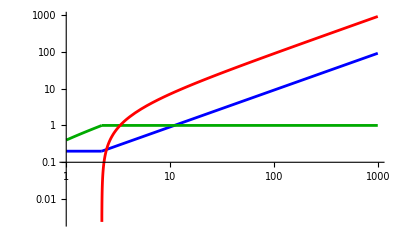

```mathematica
Show[
LogLogPlot[Evaluate[{R,Subscript[Ν, 1]}/.eq0[[-2]]],{Rin,1,RinP},PlotStyle->{Blue,Darker@Green},PlotRange->{{1,1000},{0.1,All}}],
LogLogPlot[Evaluate[{R,Subscript[Ν, 1],P}/.eq0[[-1]]],{Rin,RinP,1000},PlotStyle->{Blue,Darker@Green,Red}]
]
```

## Fig 2: Without predation

```mathematica
colors={Cyan,Purple,Orange,Gray};
legend=LineLegend[Table[colors[[Log10[Rin]+1]],{Rin,{10^3,10^2,10,1}}],{"10^3","10^2","10","1"},LegendLabel->"R_in",LabelStyle->14];
```

```mathematica
ics=Join[MakeRuleList[Ν,nsp,0.01],{P->0,R->0.1}];
```

```mathematica
(* solve model for a log-spaced range of Rin's *)
m=10^-2;
Clear[Rin];
Rin:=10^Rinp;
PrintTemporary["Rin: ",Dynamic[Rin]];
dat=Table[{Rin,FindTAD},{Rinp,0,3,0.03}];
res=RuleListInterpolation[dat];
```

```mathematica
(* Fig 2A *)
Rasterize[
Show[
PlotRuleList[res,R,ScalingFunctions->{"Log","Log"},PlotRange->{0.1,All},PlotStyle->Directive[Black,Dashed]],
PlotRuleList[TotalAbundance[res],ScalingFunctions->{"Log","Log"},PlotRange->{0.1,All},PlotStyle->Directive[Black]],
Frame->True,LabelStyle->14],ImageSize->Medium,ImageResolution->500,LightDark->"Light"]
```

-Graphics-

```mathematica
(* Fig 2B — Subscript[N, i] vs Rin *)
Rasterize[
Show[
PlotRuleList[res,Table[Subscript[Ν, i],{i,1,201,1}],PlotRange->All,ScalingFunctions->{"Log","Log"}],
PlotRuleList[res,Table[Subscript[Ν, i],{i,1,201,10}],PlotStyle->{{Thickness[0.003],Black}},PlotRange->All,ScalingFunctions->{"Log","Log"}],Frame->True,LabelStyle->14],ImageSize->Medium,ImageResolution->500,LightDark->"Light"]
```

-Graphics-

```mathematica
(* Fig 2C — TADs *)
Rasterize[
Show[
Table[PlotTAD[traits,Slice[res,Rin],PlotStyle->colors[[Log10[Rin]+1]]],{Rin,{10^3,10^2,10,1}}],Frame->True,LabelStyle->14,AxesLabel->None,PlotRange->All,Epilog->Inset[legend,{45,-0.8}]]
,ImageSize->Medium,ImageResolution->500,LightDark->"Light"]
```

-Graphics-

```mathematica
(* Fig 2D — SADs *)
Rasterize[
Show[
Table[PrestonPlot[Slice[res,Rin],ShowSpecies->False,PlotStyle->colors[[Log10[Rin]+1]]],{Rin,{10^3,10^2,10,1}}],PlotRange->{-0.001,All},Frame->True,LabelStyle->14,AxesLabel->None,Epilog->Inset[legend,{3.5,0.09}]]
,ImageSize->Medium,ImageResolution->500,LightDark->"Light"]
```

-Graphics-

## Fig 3: With predation

```mathematica
colors={Cyan,Purple,Orange,Gray};
legend=LineLegend[Table[colors[[Log10[Rin]+1]],{Rin,{10^3,10^2,10,1}}],{"10^3","10^2","10","1"},LegendLabel->"R_in",LabelStyle->12];
```

```mathematica
ics=Join[MakeRuleList[Ν,nsp,0.01],{P->0.1,R->0.1}];
```

```mathematica
m=10^-2;
Clear[Rin];
Rin:=10^Rinp;
PrintTemporary["Rin: ",Dynamic[Rin]];
dat=Table[{Rin,FindTAD},{Rinp,0,3,0.03}];
res=RuleListInterpolation[dat];
```

```mathematica
(* Fig 3A *)
Rasterize[
Show[
PlotRuleList[res,{R,P},ScalingFunctions->{"Log","Log"},PlotRange->{0.1,All},PlotStyle->{Directive[Black,Dashed],Red}],
PlotRuleList[TotalAbundance[res],ScalingFunctions->{"Log","Log"},PlotRange->{0.1,All},PlotStyle->Directive[Black]],Frame->True,LabelStyle->14
],ImageSize->Medium,ImageResolution->500,LightDark->"Light"]
```

-Graphics-

```mathematica
(* Fig 3B – Subscript[N, i] vs Rin *)
Rasterize[
Show[
PlotRuleList[res,Table[Subscript[Ν, i],{i,1,201,1}],PlotRange->All,ScalingFunctions->{"Log","Log"}],
PlotRuleList[res,Table[Subscript[Ν, i],{i,1,201,10}],PlotStyle->{{Thickness[0.003],Black}},PlotRange->All,ScalingFunctions->{"Log","Log"}],LabelStyle->14,GridLines->{{.75},None},GridLinesStyle->Directive[Black,Dashed],Frame->True]
,ImageSize->Medium,ImageResolution->500, LightDark->"Light"]
```

-Graphics-

```mathematica
(* Fig 3C — TADs *)
Rasterize[
Show[
Table[PlotTAD[traits,Slice[res,Rin],PlotStyle->colors[[Log10[Rin]+1]]],{Rin,{10^3,10^2,10,1}}],Frame->True,LabelStyle->14,AxesLabel->None,PlotRange->{All,{-22,1.5}},Epilog->Inset[legend,{46,-4.5}]],ImageSize->Medium,ImageResolution->500,LightDark->"Light"]
```

-Graphics-

```mathematica
(* Fig 3D — SADs *)
Rasterize[
Show[
Table[PrestonPlot[Slice[res,Rin],ShowSpecies->False,PlotStyle->colors[[Log10[Rin]+1]]],{Rin,(*{1,10,10^2,10^3}*){10^3,10^2,10,1}}],
PlotRange->{-0.001,All},Frame->True,LabelStyle->14,AxesLabel->None,Epilog->Inset[legend,{-2,0.09}]]
,ImageSize->Medium,ImageResolution->500, LightDark->"Light"]
```

-Graphics-

## Fig 4: Varying local environment E

#### Legend

```mathematica
colors={Red,Orange,RGBColor[{255,211,0}/255],Darker@Green,Blue,Purple};
labels={"TraditionalForm`E = 0","Cell["E",FontSlant->"Italic",ExpressionUUID->"6d53740a-8140-4c18-af32-663ff7f6277f"] = 5","E = 10","E = 15","E = 20","E = 25"};
Rasterize[SwatchLegend[colors,labels],ImageResolution->500,LightDark->"Light"]
```

-Graphics-

### m=10^-3

```mathematica
m=10^-3;
```

```mathematica
(* fixed PlotRange *)
Clear[Ε,i];
i=7;Show[Table[i--;PlotTAD[traits,FindTAD,PlotStyle->colors[[i]]],{Ε,25,0,-5}],Frame->True,LabelStyle->18,PlotRange->{Log[10^-8],Log[1]},Axes->False]
i=0;Show[Table[i++;PrestonPlot[FindTAD,Bandwidth->{"Adaptive",1,0.8},PlotStyle->colors[[i]],ShowSpecies->False],{Ε,0,25,5}],Frame->True,LabelStyle->18,PlotRange->{{Log[10^-8],Log[1]},{-0.01,1}},Axes->False]
```

-Graphics-

-Graphics-

### m=10^-2

```mathematica
m=10^-2;
```

```mathematica
(* fixed PlotRange *)
Clear[Ε,i];
i=7;Show[Table[i--;PlotTAD[traits,FindTAD,PlotStyle->colors[[i]]],{Ε,25,0,-5}],Frame->True,LabelStyle->18,PlotRange->{Log[10^-8],Log[1]},Axes->False]
i=0;Show[Table[i++;PrestonPlot[FindTAD,Bandwidth->{"Adaptive",1,0.8},PlotStyle->colors[[i]],ShowSpecies->False],{Ε,0,25,5}],Frame->True,LabelStyle->18,PlotRange->{{Log[10^-8],Log[1]},{-0.01,1}},Axes->False]
```

-Graphics-

-Graphics-

### m=10^-1

```mathematica
m=10^-1;
```

```mathematica
(* fixed PlotRange *)
Clear[Ε,i];
i=7;Show[Table[i--;PlotTAD[traits,FindTAD,PlotStyle->colors[[i]]],{Ε,25,0,-5}],Frame->True,LabelStyle->18,PlotRange->{Log[10^-8],Log[1]},Axes->False]
i=0;Show[Table[i++;PrestonPlot[FindTAD,Bandwidth->{"Adaptive",1,0.8},PlotStyle->colors[[i]],ShowSpecies->False],{Ε,0,25,5}],Frame->True,LabelStyle->18,PlotRange->{{Log[10^-8],Log[1]},{-0.01,1}},Axes->False]
```

-Graphics-

-Graphics-

### m=1

```mathematica
m=1;
```

```mathematica
(* fixed PlotRange *)
Clear[Ε,i];
i=7;Show[Table[i--;PlotTAD[traits,FindTAD,PlotStyle->colors[[i]]],{Ε,25,0,-5}],Frame->True,LabelStyle->18,PlotRange->{Log[10^-8],Log[1]},Axes->False]
i=0;Show[Table[i++;PrestonPlot[FindTAD,Bandwidth->{"Adaptive",1,0.8},PlotStyle->colors[[i]],ShowSpecies->False],{Ε,0,25,5}],Frame->True,LabelStyle->18,PlotRange->{{Log[10^-8],Log[1]},{-0.01,1}},Axes->False]
```

-Graphics-

-Graphics-

### m=10

```mathematica
m=10;
```

```mathematica
(* fixed PlotRange *)
Clear[Ε,i];
i=7;Show[Table[i--;PlotTAD[traits,FindTAD,PlotStyle->colors[[i]]],{Ε,25,0,-5}],Frame->True,LabelStyle->18,PlotRange->{Log[10^-8],Log[1]},Axes->False]
i=0;Show[Table[i++;PrestonPlot[FindTAD,Bandwidth->{"Adaptive",1,0.8},PlotStyle->colors[[i]],ShowSpecies->False],{Ε,0,25,5}],Frame->True,LabelStyle->18,PlotRange->{{Log[10^-8],Log[1]},{-0.01,1}},Axes->False]
```

-Graphics-

-Graphics-

## Fig 5: E_R-E vs. m

```mathematica
Ε:=ΕR-diff;
m:=10^mp;
```

```mathematica
Dynamic[{diff,mp}]
```

```mathematica
boundary=Quiet@ContourPlot[1.5==Length@SplitPeaks[Table[Subscript[Ν, i],{i,nsp}]/.FindTAD],{mp,-3,1},{diff,0,25},ContourStyle->Black,MaxRecursion->4];
```

```mathematica
res=Table[
tad=FindTAD;
peaks=SplitPeaks[Table[Subscript[Ν, i],{i,nsp}]/.tad];  
numpeaks=Length[peaks];
Which[
numpeaks==1,
meantrait=x/.TraitMean[traits,tad];
{numpeaks,{Abs[meantrait-ΕR],Abs[meantrait-Ε]},None},
numpeaks==2,
{numpeaks,None,peaks[[2,2]]/(peaks[[1,2]]+peaks[[2,2]])}
]
,{diff,0,25,0.25},{mp,-3,1,0.04}];
```

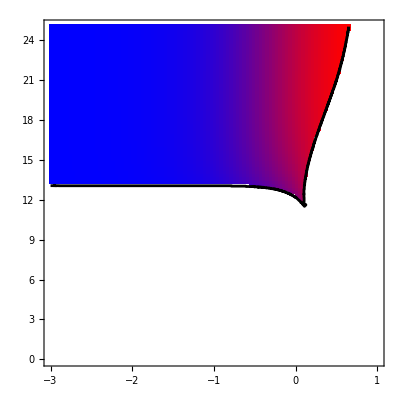

```mathematica
Show[
ContourPlot[0,{x,10^-3,10},{diff,0,25},ScalingFunctions->{"Log10",None},LabelStyle->16], ArrayPlot[res[[All,All,2]]/25,ColorFunction->(Blend[{White,Blend[{Red,Blue},#[[1]]/(#[[1]]+#[[2]]+10^-10)]},2(#[[1]]+#[[2]])]&),DataReversed->{True,False},DataRange->{{-3,1},{0,25}},AspectRatio->1],
ArrayPlot[res[[All,All,3]],ColorFunction->(Blend[{Blue,Red},#]&),DataReversed->{True,False},DataRange->{{-3,1},{0,25}},AspectRatio->1],
boundary
]
```

```mathematica
BarLegend[(Blend[{Blue,Red},#]&),LabelStyle->Directive[Black,16],"TickSide"->Left]
```

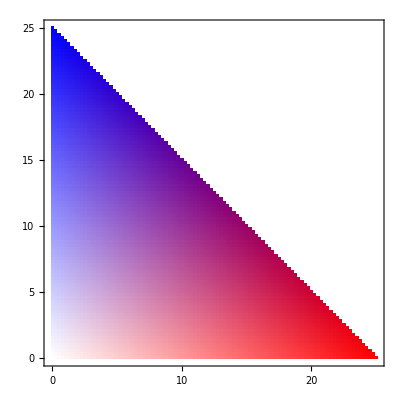

```mathematica
ArrayPlot[Reverse@Table[If[x+y<=1,{x,y},None],{x,0,1,0.01},{y,0,1,0.01}],ColorFunction->(Blend[{White,Blend[{Red,Blue},#[[1]]/(#[[1]]+#[[2]]+10^-10)]},(#[[1]]+#[[2]])]&),ColorFunctionScaling->False,FrameTicks->{True,True,False,False},DataRange->{{0,25},{0,25}},LabelStyle->Directive[Black,30],Frame->{True,True,False,False}]
```

## Supplement S1: Approximations

#### Common parameters

```mathematica
Ε=25; (* local environment *)
dN=0.2; (* consumer death rate *)
σ=5; (* width of environment-response curve *)
μmax=1; (* consumer max growth rate *)
c=0.1; (* predation rate *)
a=0.1; (* resource supply rate *)
dP=0.1; (* predator death rate *)
nsp=401; (* number of species *)
{xmin,xmax}={0,50};
σR=7; (* width of regional TAD *)
ρ:=(nsp-1)/(xmax-xmin); (* species density function *)
z=N@Sum[1/(Sqrt[2 π]σR) E^(-(x-ΕR)^2/(2 σR^2)),{x,xmin,xmax,1/ρ}];(* Normalization constant*)
ΕR=25; (* average regional environment *)
ΝRtot=1; (* regional abundance *)
```

#### No predation

```mathematica
ics=Join[MakeRuleList[Ν,nsp,0.01],{P->0,R->0.1}];
Γ0:=(m nR[Ε]2σ^2 π μmax)/(a(μmax Rin-dN));
napprox[x_]:=(m nR[x])/(m+dN-μ[x,Ε]((m+dN)/(μmax(1+ Γ0^2/(2σ^2)))))
napproxnaive[x_]:=(m nR[x])/(m+dN-μ[x,Ε]((dN+m)/μmax));
Νapprox[x_]:=napprox[x]/ρ; (* simple n-to-Ν conversion *)
Νapprox2[x_?NumericQ]:=NIntegrate[napprox[x′],{x′,x-1/(2ρ),x+1/(2ρ)}];
```

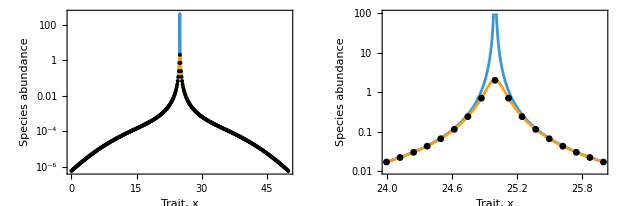

```mathematica
m=10^-2;
Rin=10;
sol=FindTAD;

Legended[GraphicsRow[{
Show[
LogPlot[{napproxnaive[x]/ρ,Νapprox[x]},{x,0,50},PlotRange->All,PlotPoints->10,FrameLabel->{"Trait, x","Species abundance"}],
PlotTAD[traits,sol,Joined->False,PlotStyle->Black,PlotMarkers->{Automatic,4}]
,Frame->True,FrameStyle->Black],
Show[
LogPlot[{napproxnaive[x]/ρ,Νapprox[x]},{x,24,26},PlotRange->{{24,26},{10^-2,100}},FrameLabel->{"Trait, x","Species abundance"}],
PlotTAD[traits,sol,Joined->False,PlotStyle->Black,PlotMarkers->{Automatic,7}],
Frame->True,FrameStyle->Black]
}, Spacings->10],SwatchLegend[{Directive[Black,PointSize[0.02]],ColorData[97][1],ColorData[97][2]},{"Simulation","High R_in limit","Cauchy approx"},LegendMarkers->{Graphics[{Disk[]}],None,None}]]
```

#### With predation

```mathematica
Ν0:=dP/c;
R0:=a Rin/(a+μmax Ν0);
Γ0:=(π m nR[Ε] *2σ^2)/(μmax R0 Ν0); 
napprox[x_]:=m nR[x]/((μmax-μ[x,Ε]+μmax Γ0^2/(2σ^2))R0);
napproxmax[x_]:=(m nR[x])/((μmax -μ[x,Ε])R0)/.{R0->(a Rin)/(a +dP/c μmax)}
Νapprox[x_]:=napprox[x]/ρ; (* simple n-to-Ν conversion *)
```

```mathematica
m=10^-2;
Rin=10;
ics=Join[MakeRuleList[Ν,nsp,0.01],{P->0.1,R->0.1}];
sol=FindTAD;
```

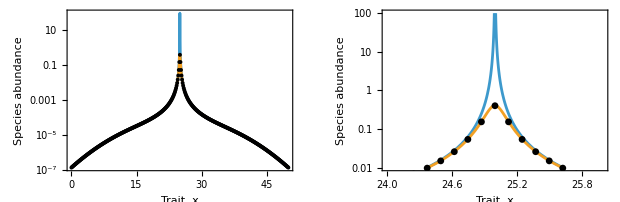

```mathematica
Legended[GraphicsRow[{
Show[
LogPlot[{napproxmax[x]/ρ,Νapprox[x]},{x,0,50},PlotRange->All,PlotPoints->10,FrameLabel->{"Trait, x","Species abundance"}],
PlotTAD[traits,sol,Joined->False,PlotStyle->Black,PlotMarkers->{Automatic,4}]
,Frame->True,FrameStyle->Black],
Show[
LogPlot[{napproxmax[x]/ρ,Νapprox[x]},{x,24,26},PlotRange->{{24,26},{10^-2,100}},FrameLabel->{"Trait, x","Species abundance"}],
PlotTAD[traits,sol,Joined->False,PlotStyle->Black,PlotMarkers->{Automatic,7}],
Frame->True,FrameStyle->Black]
}, Spacings->10],SwatchLegend[{Directive[Black,PointSize[0.02]],ColorData[97][1],ColorData[97][2]},{"Simulation","High R_in limit","Cauchy approx"},LegendMarkers->{Graphics[{Disk[]}],None,None}]]
```

## Appendix A: Evenness

```mathematica
evenness[list_]:=1/Length[list]*Exp[-Total@Table[i*Log[i],{i,list/Total[list]}]];
```

```mathematica
m=10^-1;
Ε=ΕR=25; (* local temperature *)
σ=σR=7;
dN=0.2; (* phyto death rate *)
c=0.1;
μmax=1; (* phyto max growth rate *)
a=0.1; (* resource supply rate *)
dP=0.1; (* zooplankton death rate *)
{xmin,xmax}={0,50};
ρ:=(nsp-1)/(xmax-xmin); (* species density function *)
nsp=401; (* number of species *)
ΝRtot=1;
traits=MakeRuleList[x,nsp,{xmin,xmax}];(* regional abundance *)
```

```mathematica
Rmin=-1.5;
Rmax=3;
step=0.15;
ics=Join[MakeRuleList[Ν,nsp,0.01],{P->0.1,R->0.1}];
wp=
Table[Rin=10^i;
sad=Table[Subscript[Ν, i],{i,1,nsp}]/.FinalSlice[EcoSim[traits,ics,10^8]];{Rin,evenness[sad]},{i,Rmin,Rmax,step}];
```

```mathematica
ics=Join[MakeRuleList[Ν,nsp,0.01],{P->0.,R->0.1}];
wop=
Table[Rin=10^i;
sad=Table[Subscript[Ν, i],{i,1,nsp}]/.FinalSlice[EcoSim[traits,ics,10^8]];{Rin,evenness[sad]},{i,Rmin,Rmax,step}];
```

```mathematica
Rasterize[Legended[Show[{ListPlot[wop,PlotStyle->Black,Joined->True,ScalingFunctions->{"Log",None}],ListPlot[wp,PlotStyle->Directive[Black,Dashed],Joined->True,ScalingFunctions->{"Log",None}]},PlotRange->{All,All},LabelStyle->15,Frame->True,AspectRatio->1,FrameLabel->{"Resource supply, R_in","Community evenness"},FrameStyle->Black],Placed[LineLegend[{Black,Dashed},{"Without predators","With predators"},LegendMarkers->{None,None},LegendMarkerSize->15],{0.75,0.75}]],ImageSize->Large,ImageResolution->500,LightDark->"Light"]
```

-Graphics-